# BlockSize

```mathematica
thisDirectory=If[TrueQ[StringQ[$InputFileName]&&$InputFileName=!=""&&FileExistsQ[$InputFileName]],DirectoryName[$InputFileName],Directory[]];
```

```mathematica
$rawDataFiles = <| "Crux" ->{FileNameJoin[{thisDirectory,"raw_data", "crux", "Tangram_daxpy_full.json"}]}|>;
$rawMachineDataFiles = $rawDataFiles["Crux"];
rawdata = Table[
		  Module[{info, key = "TANGRAM_CUDA_AXPY"}, 
			info = Import[rawDataFile, "RAWJSON"]; 
			info["benchmarks"] = Append[#, "key" -> key]& /@info["benchmarks"];
			Append[info, "name" ->key]
                 ], 
{rawDataFile, $rawMachineDataFiles}];
groupedData = GroupBy[Flatten[Lookup[rawdata, "benchmarks"]], Lookup[{"N", "GRID_SIZE", "BLOCK_SIZE"}]];
```

```mathematica
Union[Flatten[Lookup[#,"N"]&/@Lookup[rawdata,"benchmarks"]]]
```

{256.,512.,1024.,2048.,4096.,8192.,16384.,32768.,65536.,131072.,262144.,524288.,1.04858×10^6,2.09715×10^6,4.1943×10^6,8.38861×10^6,1.67772×10^7,3.35544×10^7}

```mathematica
32768
```

```mathematica
data=groupedData;(*Take[groupedData,UpTo[100]];*)
```

```mathematica
fullData=KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"Flops"]/10^9]],data];
firstData=KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[3]]==32&],First];
grid1Data=Flatten[Values/@Values[firstData]];
grid2Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[3]]==64&],First]]];
grid3Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥ 1000&&#[[1]]<1000000&&#[[3]]==128&],First]]];
grid4Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[3]]==256&],First]]];
grid5Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[3]]==512&],First]]];
grid6Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[3]]==1024&],First]]];
keys=Fold[StringJoin[ToString[TraditionalForm[#1]]<>"×"<>ToString[TraditionalForm[#2]]]&]/@DeleteDuplicates[Map[Delete[#,3]&,Keys[KeySortBy[firstData,First]]]];
```

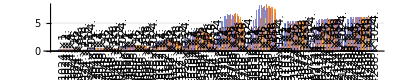

```mathematica
BarChart[Thread[{grid1Data,grid2Data, grid3Data, grid4Data, grid5Data, grid6Data}],ChartLabels->{Placed[keys,Automatic,Rotate[#,90Degree]&],None},ChartLegends->{"32","64", "128", "256", "512", "1024"},BarSpacing->{Automatic,1},PlotTheme->"Grid",AspectRatio->1/5,ImageSize->Scaled[0.75](*,ScalingFunctions->"Log"*)]
```

```mathematica
ListLinePlot[MapThread[Callout[Legended[MapIndexed[{2^First[#2+7],#1}&,#1],#2],#2]&,{Transpose[Partition[grid3Data,11]],("Bize="<>ToString[#]&)/@(2^Range[0,10])}],InterpolationOrder->5,PlotTheme->"Detailed",PlotStyle->Thick,PlotRange->Full,ImagePadding->{{100, 200}, {100, 100}}]
```

-Graphics-

```mathematica
Thread[Callout[Transpose[Partition[grid1Data,11]],2^Range[0,10]]]//Length
```

11

```mathematica
ListLinePlot[MapThread[Callout[Legended[MapIndexed[{2^First[#2+7],#1}&,#1],#2],#2]&,{Transpose[Partition[grid1Data,11]],("g1-"<>ToString[#]&)/@(2^Range[0,10])}],InterpolationOrder->5,PlotTheme->"Detailed",PlotStyle->Thick,PlotRange->Full,ImagePadding->{{100, 100}, {100, 100}}]
```

-Graphics-

```mathematica
Thread[Callout[Transpose[Partition[grid1Data,11]],("g1-"<>ToString[#]&)/@(2^Range[0,10])]]
```

{Callout[{0.0466502,0.0709488,0.0954193,0.114681,0.12817,0.134975,0.139515,0.141749,0.107302,0.093405,0.0936488,0.0928949},g1-1],Callout[{0.0551322,0.0939508,0.142136,0.1905,0.229695,0.255592,0.270102,0.279072,0.207254,0.185741,0.186635,0.18494},g1-2],Callout[{0.0616761,0.111866,0.183344,0.27892,0.378415,0.456045,0.509014,0.540323,0.407186,0.366392,0.369044,0.367901},g1-4],Callout[{0.0645523,0.122791,0.226833,0.37762,0.572182,0.763924,0.917774,1.01862,0.72496,0.70388,0.712774,0.714438},g1-8],Callout[{0.0607071,0.119356,0.242342,0.440503,0.734369,1.11568,1.48994,1.80727,1.37278,1.31945,1.33877,1.35802},g1-16],Callout[{0.0632829,0.120529,0.254738,0.488197,0.873276,1.42918,2.22697,3.01307,2.49396,2.32906,2.3901,2.44311},g1-32],Callout[{0.0625341,0.125085,0.247544,0.495387,0.950324,1.72354,2.90768,4.35166,3.91824,3.71079,4.00589,4.12079},g1-64],Callout[{0.0600186,0.120813,0.241146,0.484532,0.954303,1.80994,3.35482,5.55938,5.75172,4.92155,5.39996,5.73112},g1-128],Callout[{0.0552925,0.111704,0.220449,0.439148,0.879077,1.77949,3.38562,6.07548,7.32943,5.25259,5.66485,5.91618},g1-256],Callout[{0.0469916,0.0955193,0.193236,0.388818,0.754916,1.53743,3.09715,5.65119,7.10522,5.28683,5.68457,5.9036},g1-512],Callout[{0.0364212,0.0733776,0.145796,0.288635,0.570598,1.17222,2.30919,4.57396,6.98237,5.27177,5.71101,5.96587},g1-1024]}

```mathematica
ListLinePlot[
Join[
MapThread[Callout[Legended[MapIndexed[{2^First[#2+7],#1}&,#1],#2],#2]&,{Transpose[Partition[grid1Data,11]],("g1-"<>ToString[#]&)/@(2^Range[0,10])}],
MapThread[Callout[Legended[MapIndexed[{2^First[#2+7],#1}&,#1],#2],#2]&,{Transpose[Partition[grid2Data,11]],("g2-"<>ToString[#]&)/@(2^Range[0,10])}]
]
,InterpolationOrder->5,PlotTheme->"Detailed",PlotRange->Full,ImagePadding->{{Automatic, 300}, {Automatic, Automatic}},ImageSize->Scaled[0.75],
PlotStyle->"Rainbow",AspectRatio->1/2
]
```

-Graphics-

# GridSize

```mathematica
thisDirectory=If[TrueQ[StringQ[$InputFileName]&&$InputFileName=!=""&&FileExistsQ[$InputFileName]],DirectoryName[$InputFileName],Directory[]];
```

```mathematica
$rawDataFiles = <| "Crux" ->{FileNameJoin[{thisDirectory,"raw_data", "crux", "Tangram_daxpy_full.json"}]}|>;
$rawMachineDataFiles = $rawDataFiles["Crux"];
rawdata = Table[
		  Module[{info, key = "TANGRAM_CUDA_AXPY"}, 
			info = Import[rawDataFile, "RAWJSON"]; 
			info["benchmarks"] = Append[#, "key" -> key]& /@info["benchmarks"];
			Append[info, "name" ->key]
                 ], 
{rawDataFile, $rawMachineDataFiles}];
groupedData = GroupBy[Flatten[Lookup[rawdata, "benchmarks"]], Lookup[{"N", "GRID_SIZE", "BLOCK_SIZE"}]]
```

<|{256.,1.,32.}→{<|name→TANGRAM_CUDA_AXPY<double, 1, 32>/256/manual_time,iterations→108262,real_time→5487.65,cpu_time→11535.,time_unit→ns,bytes_per_second→3.73201×10^8,items_per_second→4.66502×10^7,BLOCK_SIZE→32.,Flops→4.66502×10^7,GRID_SIZE→1.,N→256.,key→TANGRAM_CUDA_AXPY|>},1186,{3.35544×10^7,1024.,1024.}→{<|name→TANGRAM_CUDA_AXPY<double, 1024, 1024>/33554432/manual_time,iterations→132,real_time→5.30325×10^6,cpu_time→5.31313×10^6,time_unit→ns,bytes_per_second→5.06171×10^10,1,BLOCK_SIZE→1024.,Flops→6.32714×10^9,GRID_SIZE→1024.,N→3.35544×10^7,key→TANGRAM_CUDA_AXPY|>}|>
 |  |  |  |

```mathematica
data=groupedData;(*Take[groupedData,UpTo[100]];*)
```

```mathematica
fullData=KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"Flops"]/10^9]],data];
firstData=KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==1&],First];
grid1Data=Flatten[Values/@Values[firstData]];
grid2Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==2&],First]]];
grid3Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥ 1000&&#[[1]]<1000000&&#[[2]]==4&],First]]];
grid4Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]== 8&],First]]];
grid5Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==16&],First]]];
grid6Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==32&],First]]];
grid7Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==64&],First]]];
grid8Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==128&],First]]];
grid9Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==256&],First]]];
grid10Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==512&],First]]];
grid11Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[1]]≥1000&&#[[1]]<1000000&&#[[2]]==1024&],First]]];
keys=Fold[StringJoin[ToString[TraditionalForm[#1]]<>"×"<>ToString[TraditionalForm[#2]]]&]/@DeleteDuplicates[Map[Delete[#,3]&,Keys[KeySortBy[firstData,First]]]];
```

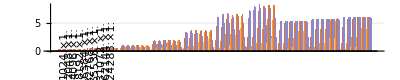

```mathematica
BarChart[Thread[{grid1Data,grid2Data, grid3Data, grid4Data, grid5Data, grid6Data,grid7Data,grid8Data,grid9Data,grid10Data,grid11Data}],ChartLabels->{Placed[keys,Automatic,Rotate[#,90Degree]&],None},ChartLegends->{"1","2", "4", "8", "16", "32", "64", "128", "256", "512", "1024"},BarSpacing->{Automatic,1},PlotTheme->"Grid",AspectRatio->1/5,ImageSize->Scaled[0.75](*,ScalingFunctions->"Log"*)]
```

# Work

```mathematica
thisDirectory=If[TrueQ[StringQ[$InputFileName]&&$InputFileName=!=""&&FileExistsQ[$InputFileName]],DirectoryName[$InputFileName],Directory[]];
```

```mathematica
$rawDataFiles = <| "Crux" ->{FileNameJoin[{thisDirectory,"raw_data", "crux", "Tangram_daxpy_fix.json"}]}|>;
$rawMachineDataFiles = $rawDataFiles["Crux"]

data = Table[
		  Module[{info, key = "TANGRAM_CUDA_AXPY"}, 
			info = Import[rawDataFile, "RAWJSON"]; 
			info["benchmarks"] = Append[#, "key" -> key]& /@Select[ info["benchmarks"],#["GRID_SIZE"]==1&];
			Append[info, "name" ->key]
                 ], 
{rawDataFile, $rawMachineDataFiles}];
data = Table[
		  Module[{info, key = "TANGRAM_CUDA_AXPY"}, 
			info = Import[rawDataFile, "RAWJSON"]; 
			info["benchmarks"] = Append[#, "key" -> key]& /@info["benchmarks"];
			Append[info, "name" ->key]
                 ], 
{rawDataFile, $rawMachineDataFiles}];
groupedData = GroupBy[Flatten[Lookup[data, "benchmarks"]], Lookup[{"N", "GRID_SIZE", "BLOCK_SIZE"}]];
```

{/home/simon/RaiBench/microbench/results/raw_data/crux/Tangram_daxpy_fix.json}

```mathematica
Dataset[groupedData]
```

Dataset[<>]

```mathematica
AssociationQ[data]
```

False

```mathematica
data=Take[groupedData,UpTo[100]];
```

```mathematica
fullData=KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"Flops"]/10^9]],data];
grid1Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[2]]==1&],Fold[Times,1,#]&]]];grid2Data=Flatten[Values/@Values[KeySortBy[KeySelect[fullData,#[[2]]==2&],Fold[Times,1,#]&]]];
keys=Fold[StringJoin[ToString[TraditionalForm[#1]]<>"×"<>ToString[TraditionalForm[#2]]]&]/@DeleteDuplicates[Map[Delete[#,2]&,Keys[KeySortBy[fullData,Fold[Times,1,#]&]]]]
```

{256.×32.,512.×32.,1024.×32.,2048.×32.,4096.×32.,8192.×32.,16384.×32.,32768.×32.,65536.×32.,131072.×32.,262144.×32.,524288.×32.,1.04858×10^6×32.,2.09715×10^6×32.,4.1943×10^6×32.,8.38861×10^6×32.,1.67772×10^7×32.,3.35544×10^7×32.}

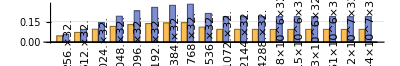

```mathematica
data=Take[groupedData,UpTo[100]];
BarChart[Thread[{grid1Data,grid2Data}],ChartLabels->{Placed[keys,Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",AspectRatio->1/6,ImageSize->Scaled[0.75](*,ScalingFunctions->"Log"*)]
```

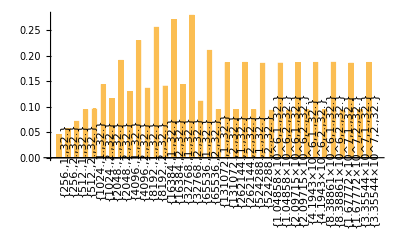

```mathematica
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"Flops"]/10^9]],data],Fold[Times,1,First[#1]]&]],PlotTheme->Automatic,ChartLabels->{Placed[Automatic,Automatic,Rotate[#1,90 °]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1}]
```

```mathematica
makeChart[data_]:=BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"Flops"]/10^9]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Automatic,Automatic,Rotate[#,90 Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",(*ScalingFunctions->"Log"*)];
```

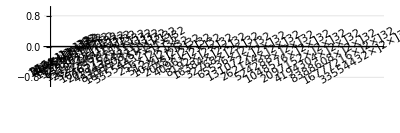

```mathematica
makeChart[data]
```

```mathematica
Keys[groupedData]
```

{{256.},{512.},{1024.},{2048.},{4096.},{8192.},{16384.},{32768.},{65536.},{131072.},{262144.},{524288.},{1.04858×10^6},{2.09715×10^6},{4.1943×10^6},{8.38861×10^6},{1.67772×10^7},{3.35544×10^7}}

```mathematica
Dataset[groupedData[{17920.,17920.,17920.}]]
```

Dataset[<>]